```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/

```mathematica
(* Thickness *)
th=0.003;
```

## Direct basis

```mathematica
p[l_,α_]:=N[l α+(1-α) IntegerPart[l/(1+α)]];
```

```mathematica
τ=N [(1+Sqrt[5])/2];
t[i_]:=p[i+1,1/τ]-p[i,1/τ]
```

```mathematica
t[5]
```

0.618034

```mathematica
(* rk: t[i] is related to IntegerPart[τ^-1( #+1)]-IntegerPart[τ^-1 #] *)
(IntegerPart[τ^-1( #+1)]-IntegerPart[τ^-1 #])&/@Range[0,4]
(IntegerPart[τ^-1( #+1)]-IntegerPart[τ^-1 #]-t[#])&/@Range[20]//Chop
```

{0,1,0,1,1}

{0,-0.618034,0,0,-0.618034,0,-0.618034,0,0,-0.618034,0,0,-0.618034,0,-0.618034,0,0,-0.618034,0,-0.618034}

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_]:=Block[{tbl,ar,Fn},
Fn=Fibonacci[n];
tbl=Table[{i,i+1}->t[i],{i,1,Fn-1}];
ar=SparseArray[tbl,{Fn,Fn}];
Normal[ar+Transpose[ar]]
]
h[6]//MatrixForm
```

(0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0.618034 | 0. | 0. | 0. | 0. | 0.
0. | 0.618034 | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.618034 | 0. | 0.
0. | 0. | 0. | 0. | 0.618034 | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.618034
0. | 0. | 0. | 0. | 0. | 0. | 0.618034 | 0.)

```mathematica
(* hamiltonien avec conditions aux bords périodiques *)
Clear[hp];
hp[n_]:=Block[{tbl,ar,Fn},
Fn=Fibonacci[n];
tbl=Table[{i,i+1}->t[i],{i,1,Fn-1}];
AppendTo[tbl,{1,Fn}->t[Fn-1]];
ar=SparseArray[tbl,{Fn,Fn}];
Normal[ar+Transpose[ar]]
]
hp[6]//MatrixForm
```

(0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.618034
1. | 0. | 0.618034 | 0. | 0. | 0. | 0. | 0.
0. | 0.618034 | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.618034 | 0. | 0.
0. | 0. | 0. | 0. | 0.618034 | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.618034
0.618034 | 0. | 0. | 0. | 0. | 0. | 0.618034 | 0.)

```mathematica
Dimensions[%50]
```

{1}

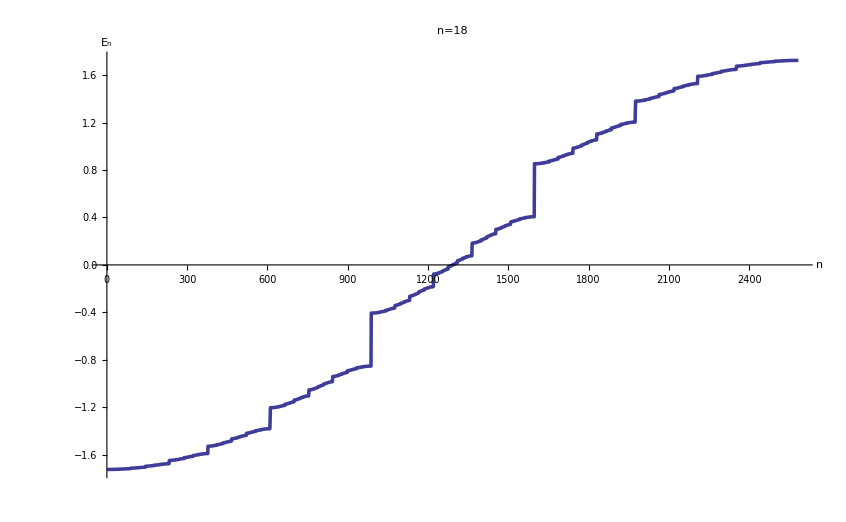

```mathematica
(* spectre *)
vp1=Block[{vp,plot,i=18},
vp=Sort[Eigenvalues[hp[i]]];
plot=ListPlot[vp,Joined->True,AxesLabel->{"n","E_n"},PlotLabel->"n="<>ToString[i],PlotStyle->Thickness[th]];
Export[dir<>"/data/spectrum_fibo_chain.png",plot];
Print[plot];
vp
];
```

## Co-numbered basis

### Hamiltonian directly written in the co basis

```mathematica
hco[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
hco[5,tw,ts]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | tw | 0 | 0 | ts | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | tw | 0 | 0 | ts | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | tw | 0 | 0 | ts | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | tw | 0 | 0 | ts | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | tw | 0 | 0 | ts
tw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | tw | 0 | 0
0 | tw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | tw | 0
0 | 0 | tw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | tw
ts | 0 | 0 | tw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ts | 0 | 0 | tw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ts | 0 | 0 | tw | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ts | 0 | 0 | tw | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ts | 0 | 0 | tw | 0 | 0 | 0 | 0 | 0)

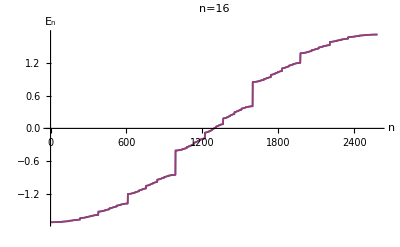

```mathematica
Block[{vp,i=16,ts=1./τ,tw=1.,plot},
vp=Sort[Eigenvalues[hco[i,tw,ts]]];
plot=ListPlot[{vp,vp1},Joined->True,AxesLabel->{"n","E_n"},PlotLabel->"n="<>ToString[i],PlotStyle->Thickness[th]];
Print[plot];
]
```

```mathematica
(* wavefunctions with standard labelling and IDoS *)
wf=Block[{val,vec,i=16,ts=1.,tw=1./10.},
{val,vec}=Eigensystem[hco[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

```mathematica
MatrixPlot [wf,FrameLabel->{"integrated density of states","amplitude in co-numbered basis"}]
Export[dir<>"/data/cobasis_idos.pdf",%];
```

-Graphics-